```mathematica
data=
Import["/Users/epersico/Google Drive/GitHub/Map Files/widths/m_1_n_2_widths.out","Table"]
```

{{0.01,0.00075},{0.02,0.0025},{0.03,0.004},{0.04,0.00425},{0.05,0.00775},{0.06,0.00575},{0.07,0.01025},{0.08,0.0095},{0.09,0.0125},{0.1,0.013},{0.11,0.01575},{0.12,0.015},{0.13,0.018},{0.14,0.015},{0.15,0.02125},{0.16,0.01875},{0.17,0.02775},{0.18,0.02775},{0.19,0.02425},{0.2,0.03325},{0.21,0.03325},{0.22,0.0295},{0.23,0.036},{0.24,0.03825},{0.25,0.042},{0.26,0.03775},{0.27,0.0455},{0.28,0.043},{0.29,0.04725},{0.3,0.0425},{0.31,0.04425},{0.32,0.04825},{0.33,0.049},{0.34,0.05175},{0.35,0.0595},{0.36,0.057},{0.37,0.0625},{0.38,0.0635},{0.39,0.067},{0.4,0.06575},{0.41,0.06075},{0.42,0.07225},{0.43,0.06925},{0.44,0.0695},{0.45,0.078},{0.46,0.075},{0.47,0.08025},{0.48,0.08225},{0.49,0.082},{0.5,0.0845},{0.51,0.0875},{0.52,0.09325},{0.53,0.0925},{0.54,0.0825},{0.55,0.0905},{0.56,0.094},{0.57,0.103},{0.58,0.10375},{0.59,0.101},{0.6,0.10975},{0.61,0.11125},{0.62,0.11025},{0.63,0.1145},{0.64,0.10375},{0.65,0.1065},{0.66,0.1215},{0.67,0.11775},{0.68,0.117},{0.69,0.12575},{0.7,0.13125},{0.71,0.12925},{0.72,0.131},{0.73,0.134},{0.74,0.12975},{0.75,0.1385},{0.76,0.129},{0.77,0.147125},{0.78,0.1485},{0.79,0.14525},{0.8,0.1465},{0.81,0.15575},{0.82,0.1465},{0.83,0.1565},{0.84,0.15775},{0.85,0.156},{0.86,0.1645},{0.87,0.165625},{0.88,0.165125},{0.89,0.172125},{0.9,0.16625},{0.91,0.17975},{0.92,0.17075},{0.93,0.165},{0.94,0.163},{0.95,0.171},{0.96,0.184},{0.97,0.16975},{0.98,0.171},{0.99,0.190375},{1.,0.18575}}

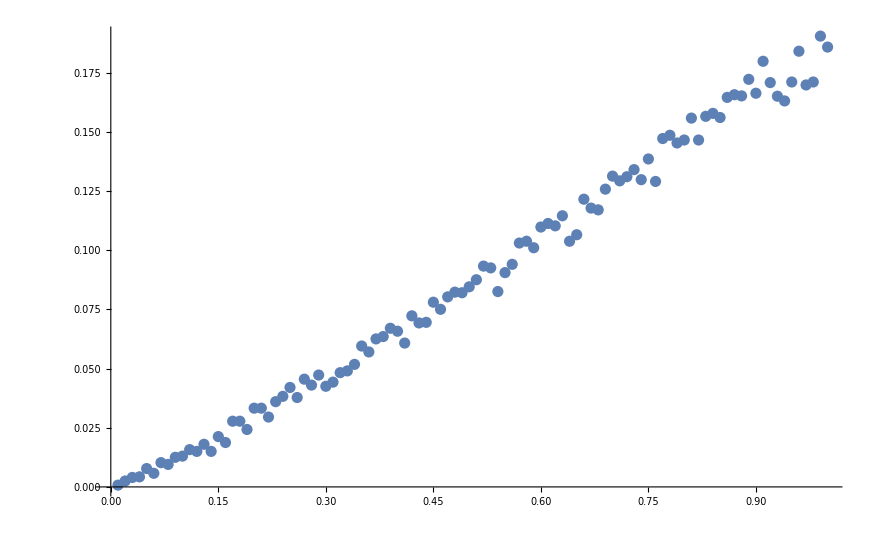

```mathematica
ListPlot[data]
```

```mathematica
logdata = data;
logdata[[All,2]] = Log[logdata[[All,2]]];
```

```mathematica
0.35/100 
0.1/%
```

0.0035

28.5714

-6.05922+14.451 x

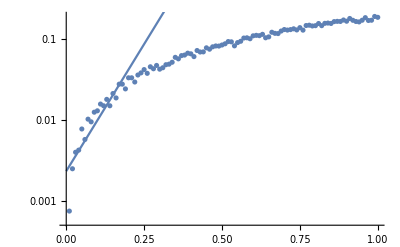

```mathematica
line1 = Fit[logdata[[1;;20,All]],{1,x},x]
Show[ListLogPlot[data],Plot[line1,{x,0,1}]]
```

FittedModel[-0.000931744+0.188861 x^1.13269]

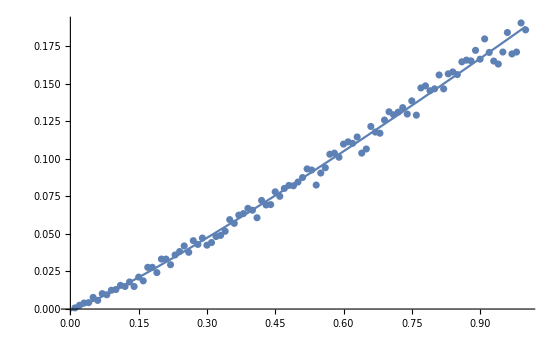

```mathematica
nlm=NonlinearModelFit[data[[All,All]],a +b x^c,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,1}]]
```

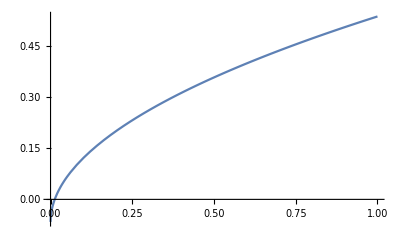

```mathematica
Plot[nlm[x],{x,0,1}]
```